```mathematica
src = Import@FileNameJoin@{NotebookDirectory[], "8-3-10-drop5_highres.png"};
```

## component

```mathematica
area = ComponentMeasurements[src, "Area"];
```

HighlightImage BUG. Highlights specified by region may move observed by src.

```mathematica
cells = ComponentMeasurements[src, {"Centroid", "EquivalentDiskRadius"}, MemberQ[#Area]@areaKeys[[;;-8]]&];
HighlightImage[src, Values[cells][[;;,1]]]
```

```mathematica
areaGroups = GroupBy[Last]@area;
areaKeys = Keys@areaGroups//Union
```

{1.,2.,2.25,3.125,4.,4.25,5.125,6.25,7.125,8.25,8.375,8.5,9.375,9.5,10.25,10.375,10.5,10.625,11.375,11.5,12.25,12.375,13.25,42.5,48.125,51.5,52.25,407.,421.875,438.875,441.625,37963.8,38062.6,60309.,60408.6,328016.,331176.,331182.}

```mathematica
Last/@Tally@ClusteringComponents@areaKeys
```

{22,5,4,4,3}

```mathematica
MinMax@Values@Pick[area, clusters, #]&/@Union@clusters
```

{{9.375,331182.},{1.,7.125},{8.25,8.5}}

```mathematica
(*clusters = ClusteringComponents[Values@area, DistanceFunction->Function[(#1-#2)^2], CriterionFunction->"StandardDeviation"]*)
```

```mathematica
clusters = ClusteringComponents[Values@area]
```

```mathematica
Pick[area, clusters, 1]
Pick[area, clusters, 2]
Pick[area, clusters, 3]
```

{1→331176.,2→331176.,3→10.375,4→10.375,5→37963.8,6→10.375,7→10.375,8→12.25,9→12.25,10→10.375,11→10.375,14→10.375,15→10.375,16→10.375,17→10.375,18→10.375,19→10.375,20→10.375,21→10.375,22→10.375,25→10.375,26→10.375,27→10.375,28→10.375,29→10.375,34→10.375,35→12.25,36→12.25,37→10.375,38→10.375,39→10.375,40→10.375,41→10.375,42→10.375,43→10.375,44→10.375,45→10.375,46→42.5,47→10.375,48→12.25,49→12.25,50→10.375,51→51.5,66→11.375,67→10.5,69→11.375,71→11.375,72→11.375,73→11.375,74→11.375,75→11.5,76→10.25,77→11.375,78→11.375,79→11.375,80→11.375,81→38062.6,82→13.25,83→9.5,85→12.375,87→9.5,88→9.5,90→52.25,92→60408.6,93→9.5,94→11.375,95→11.375,97→421.875,98→10.25,99→48.125,100→9.5,101→11.375,102→11.375,106→10.25,107→11.375,108→38062.6,114→441.625,117→10.375,118→10.375,121→10.375,122→10.375,123→10.375,124→10.375,125→60309.,126→11.375,127→9.5,128→10.25,130→10.625,131→9.375,132→11.375,133→11.375,134→11.375,140→11.375,141→9.5,143→9.5,145→11.375,146→10.25,147→10.25,148→11.375,149→9.5,150→10.25,151→13.25,154→10.25,155→10.25,157→9.5,158→11.375,160→10.25,161→9.5,167→407.,168→10.375,171→10.375,172→10.375,175→10.375,176→10.375,177→438.875,178→10.375,182→10.25,183→10.25,185→10.25,186→10.25,187→9.5,190→11.5,191→9.5,195→10.5,196→9.5,199→9.5,200→9.5,209→9.5,210→9.375,211→10.25,212→12.375,213→11.5,214→9.5,215→9.5,216→11.5,217→11.375,221→10.375,222→10.375,223→10.375,224→10.375,225→10.375,226→10.375,227→10.375,228→10.375,229→11.375,230→60309.,231→12.375,232→10.375,233→12.25,234→11.375,235→12.25,236→10.375,237→60408.6,241→10.25,243→10.375,244→10.375,249→12.25,250→10.375,251→10.375,252→10.375,253→10.375,254→12.25,255→11.375,256→9.5,257→11.375,258→11.375,260→9.5,261→11.375,263→11.375,264→11.375,265→9.5,267→10.375,268→10.375,271→10.375,272→10.375,273→10.375,274→10.375,275→10.375,276→10.375,283→438.875,284→10.375,285→10.375,286→10.375,287→10.375,288→407.,290→10.375,291→10.375,292→9.5,293→9.5,294→10.375,295→10.375,297→11.375,298→11.375,301→11.375,302→11.375,304→9.5,305→10.5,308→10.5,309→9.5,311→10.375,312→11.375,313→11.375,315→11.5,316→10.375,318→10.25,319→11.375,320→11.375,321→10.375,322→10.375,323→9.5,331→10.375,332→10.375,333→328016.,334→10.375,335→10.375,337→10.375,338→10.375,341→10.375,342→10.375,345→10.375,346→10.375,348→9.5,350→11.375,351→48.125,352→52.25,358→10.375,359→10.375,360→10.375,361→10.375,362→12.25,363→12.25,364→12.25,365→12.25,366→10.375,367→10.375,368→10.375,369→10.375,374→10.375,375→10.375,376→10.375,377→10.375,383→9.5,385→12.25,386→10.375,387→9.5,388→10.375,389→12.25,393→10.375,394→10.375,395→10.375,396→10.375,397→10.375,398→51.5,399→10.375,400→10.375,401→42.5,402→10.375,403→10.25,405→10.375,406→10.375,407→11.375,408→10.375,409→10.375,411→10.375,412→10.375,413→10.375,414→10.375,417→37963.8,419→12.25,420→10.375,421→10.375,422→12.25,424→37963.8,425→10.25,427→10.375,428→10.375,429→11.375,433→10.375,434→10.375,438→10.625,439→12.25,440→12.25,441→10.375,442→10.375,443→10.375,444→10.375,445→10.375,446→10.375,447→12.25,448→12.25,449→10.375,451→10.375,453→9.5,460→9.5,462→9.5,465→9.5,466→441.625,468→10.375,469→10.375,470→421.875,471→10.375,472→10.375,473→10.375,474→10.375,475→10.375,476→10.375,477→10.5,479→10.25,484→9.5,485→10.375,486→10.375,487→10.375,488→10.375,489→10.375,492→10.375,493→10.5,496→11.375,497→9.5,498→10.25,499→10.375,500→10.375,502→9.375,504→10.375,505→10.375,506→11.375,513→10.375,514→12.25,515→12.25,516→10.375,517→11.375,518→10.25,521→9.5,522→10.25,523→11.375,525→11.375,526→11.375,528→11.375,531→10.25,533→11.375,534→11.375,535→9.5,536→9.5,537→11.375,538→11.375,539→11.375,540→9.5,541→11.375,542→11.375,543→12.375,544→11.5,545→10.25,546→10.25,547→9.375,548→11.375,549→10.375,550→10.375,551→10.375,552→10.375,553→331176.,554→331182.,555→11.375,556→9.375,557→10.25,558→10.25,559→11.5,560→12.375,561→11.375,562→11.375,563→9.5,564→11.375,565→11.375,566→11.375,567→9.5,568→9.5,569→11.375,570→11.375,572→11.375,573→10.25,577→11.375,578→60408.6,579→11.375,580→11.375,581→11.375,583→10.25,584→60309.,585→9.5,588→10.25,589→10.375,590→12.25,591→12.25,592→10.375,597→11.375,602→10.375,603→10.375,604→9.375,605→10.375,606→10.375,607→10.25,608→9.5,609→11.375,610→10.5,613→10.375,615→10.375,617→10.375,618→10.375,619→10.375,620→10.375,621→9.5,626→441.625,627→10.25,629→10.5,630→421.875,631→10.375,632→10.375,633→10.375,634→10.375,635→10.375,636→10.375,637→10.375,638→10.375,639→9.5,640→9.5,642→9.5,647→10.375,652→9.5,656→10.375,657→12.25,658→12.25,659→10.375,660→10.375,661→10.375,662→10.375,663→10.375,664→10.375,665→12.25,666→12.25,667→10.375,668→10.375,669→10.625,676→11.375,677→10.375,678→10.375,680→10.25,681→12.25,682→10.375,683→10.375,684→12.25,687→10.375,688→10.375,691→10.375,692→10.375,694→11.375,695→10.375,696→42.5,697→10.375,698→10.375,699→51.5,700→10.375,702→10.25,703→10.375,704→10.375,705→10.375,706→10.375,707→10.375,708→10.375,709→10.375,710→10.375,713→12.25,714→10.375,715→60309.,716→60408.6,718→9.5,719→10.375,720→12.25,721→9.5,724→10.375,725→10.375,726→10.375,727→10.375,736→10.375,737→10.375,738→10.375,739→10.375,740→12.25,741→12.25,742→12.25,743→12.25,744→10.375,745→10.375,746→10.375,747→10.375,748→52.25,749→48.125,755→11.375,757→10.375,758→10.375,759→10.375,760→10.375,761→10.375,762→9.5,768→10.375,770→10.375,771→10.375,772→10.375,773→10.375,774→10.375,775→10.375,776→10.375,777→9.5,785→11.375,786→11.375,787→10.25,789→10.375,790→11.5,792→11.375,793→11.375,795→38062.6,796→9.5,797→407.,798→10.5,801→10.5,802→9.5,803→11.375,804→11.375,808→438.875,809→11.375,810→38062.6,811→11.375,812→10.375,813→10.375,814→9.5,815→9.5,816→10.375,818→10.375,820→10.375,821→10.375,822→10.375,823→10.375,824→10.375,827→10.375,828→10.375,831→10.375,832→10.375,835→10.375,836→10.375,839→10.375,841→9.5,842→11.375,843→11.375,844→11.375,846→9.5,848→11.375,849→11.375,850→9.5,851→11.375,852→12.25,853→10.375,854→10.375,855→10.375,856→10.375,857→12.25,858→10.375,863→10.375,865→10.25,868→11.375,870→10.375,871→12.25,872→12.375,873→12.25,874→10.375,875→11.375,876→10.375,877→10.375,878→10.375,879→10.375,880→10.375,881→10.375,882→10.375,883→10.375,885→11.375,888→11.5,889→9.5,890→9.5,891→11.5,892→12.375,893→10.25,894→9.375,895→9.5,901→9.5,903→9.5,908→9.5,909→10.5,913→9.5,914→438.875,915→11.5,918→9.5,919→10.25,920→10.25,923→10.25,924→10.25,926→407.,928→10.375,929→10.375,930→10.375,931→10.375,932→10.375,933→10.375,939→9.5,940→10.25,941→11.375,947→9.5,949→10.25,950→10.25,951→13.25,952→10.25,953→9.5,954→11.375,956→10.25,957→10.25,958→11.375,961→9.5,963→9.5,964→11.375,965→11.375,969→11.375,971→11.375,972→10.625,974→9.5,975→9.375,977→10.25,978→11.375,979→10.375,980→10.375,981→10.375,982→10.375,983→10.375,985→421.875,986→441.625,988→10.375,989→48.125,990→52.25,995→11.375,997→11.375,998→11.375,999→9.5,1001→11.375,1003→10.25,1006→10.25,1008→11.375,1009→9.5,1012→9.5,1013→9.5,1014→12.375,1016→9.5,1017→13.25,1018→11.375,1021→11.375,1022→11.375,1023→11.375,1024→10.25,1025→11.5,1026→11.375,1027→11.375,1028→11.375,1029→11.375,1030→11.375,1031→10.5,1032→11.375,1049→51.5,1050→37963.8,1051→10.375,1052→12.25,1053→12.25,1054→10.375,1055→42.5,1056→10.375,1057→10.375,1058→10.375,1059→10.375,1060→10.375,1061→10.375,1062→10.375,1063→10.375,1064→10.375,1065→12.25,1066→12.25,1067→10.375,1072→10.375,1073→10.375,1074→10.375,1075→10.375,1076→10.375,1077→10.375,1080→10.375,1081→10.375,1082→10.375,1083→10.375,1084→10.375,1085→10.375,1086→10.375,1087→10.375,1088→10.375,1091→10.375,1092→12.25,1093→12.25,1094→10.375,1095→10.375,1096→10.375,1097→10.375}

{12→6.25,13→6.25,23→6.25,24→6.25,30→6.25,31→6.25,32→6.25,33→6.25,52→6.25,53→7.125,57→6.25,58→6.25,61→4.25,63→3.125,65→6.25,68→4.,70→6.25,96→6.25,109→6.25,110→3.125,111→5.125,112→2.,113→3.125,115→2.,116→1.,119→6.25,120→6.25,129→6.25,135→6.25,137→7.125,138→2.25,139→1.,152→1.,153→3.125,156→7.125,159→5.125,163→5.125,164→5.125,165→4.25,166→1.,169→6.25,170→6.25,173→6.25,174→6.25,179→6.25,180→6.25,201→7.125,206→6.25,207→7.125,218→6.25,238→6.25,245→6.25,246→6.25,247→6.25,248→6.25,262→6.25,266→6.25,269→6.25,270→6.25,277→6.25,278→6.25,279→6.25,280→6.25,281→6.25,282→6.25,289→4.25,296→5.125,314→5.125,317→4.25,324→6.25,327→3.125,329→5.125,330→6.25,336→6.25,339→6.25,340→6.25,343→6.25,344→6.25,347→6.25,354→3.125,355→1.,356→2.25,357→1.,370→6.25,371→6.25,372→6.25,373→6.25,378→6.25,379→6.25,380→6.25,381→6.25,382→1.,384→6.25,390→4.25,415→1.,416→2.,418→2.,423→3.125,430→6.25,431→6.25,432→6.25,435→6.25,436→6.25,437→6.25,450→6.25,452→5.125,455→6.25,457→6.25,458→3.125,461→4.,463→3.125,464→4.25,467→3.125,481→6.25,490→6.25,491→6.25,495→6.25,507→7.125,509→6.25,510→6.25,511→6.25,512→6.25,519→7.125,520→7.125,524→6.25,532→6.25,571→6.25,582→6.25,586→7.125,587→7.125,593→6.25,594→6.25,595→6.25,596→6.25,599→7.125,611→6.25,614→6.25,616→6.25,624→6.25,641→3.125,643→4.25,644→3.125,646→4.,648→6.25,649→3.125,650→6.25,654→5.125,655→6.25,670→6.25,671→6.25,672→6.25,673→6.25,674→6.25,675→6.25,685→3.125,686→2.,689→2.,690→1.,717→4.25,722→6.25,723→1.,728→6.25,729→6.25,730→6.25,731→6.25,732→6.25,733→6.25,734→6.25,735→6.25,750→1.,751→2.25,753→1.,754→3.125,763→6.25,764→6.25,765→6.25,766→6.25,767→6.25,769→6.25,778→6.25,779→5.125,781→3.125,784→6.25,788→4.25,791→5.125,817→5.125,819→4.25,825→6.25,826→6.25,829→6.25,830→6.25,833→6.25,834→6.25,837→6.25,838→6.25,840→6.25,845→6.25,859→6.25,860→6.25,861→6.25,862→6.25,869→6.25,887→6.25,897→7.125,898→6.25,905→7.125,925→6.25,927→6.25,934→6.25,935→6.25,936→6.25,937→6.25,942→4.25,943→5.125,944→1.,945→5.125,946→5.125,948→7.125,955→3.125,960→1.,966→7.125,968→6.25,970→2.25,973→1.,976→6.25,984→6.25,987→6.25,991→1.,992→2.,993→3.125,994→2.,1000→5.125,1002→6.25,1007→6.25,1010→3.125,1033→6.25,1034→4.,1035→6.25,1037→3.125,1039→4.25,1042→6.25,1043→6.25,1047→7.125,1048→6.25,1068→6.25,1069→6.25,1070→6.25,1071→6.25,1078→6.25,1079→6.25,1089→6.25,1090→6.25}

{54→8.25,55→8.25,56→8.25,59→8.25,60→8.25,62→8.25,64→8.25,84→8.25,86→8.375,89→8.25,91→8.375,103→8.375,104→8.25,105→8.5,136→8.375,142→8.375,144→8.375,162→8.25,181→8.25,184→8.375,188→8.25,189→8.25,192→8.25,193→8.5,194→8.375,197→8.375,198→8.5,202→8.25,203→8.25,204→8.25,205→8.25,208→8.25,219→8.375,220→8.25,239→8.375,240→8.375,242→8.375,259→8.375,299→8.25,300→8.25,303→8.375,306→8.25,307→8.25,310→8.25,325→8.25,326→8.25,328→8.25,349→8.25,353→8.25,391→8.25,392→8.375,404→8.375,410→8.25,426→8.375,454→8.25,456→8.25,459→8.375,478→8.25,480→8.25,482→8.25,483→8.375,494→8.25,501→8.25,503→8.25,508→8.375,527→8.25,529→8.375,530→8.5,574→8.5,575→8.25,576→8.375,598→8.375,600→8.25,601→8.25,612→8.25,622→8.375,623→8.25,625→8.25,628→8.25,645→8.375,651→8.25,653→8.25,679→8.375,693→8.25,701→8.375,711→8.375,712→8.25,752→8.25,756→8.25,780→8.25,782→8.25,783→8.25,794→8.25,799→8.25,800→8.25,805→8.375,806→8.25,807→8.25,847→8.375,864→8.375,866→8.375,867→8.375,884→8.25,886→8.375,896→8.25,899→8.25,900→8.25,902→8.25,904→8.25,906→8.5,907→8.375,910→8.375,911→8.5,912→8.25,916→8.25,917→8.25,921→8.375,922→8.25,938→8.25,959→8.375,962→8.375,967→8.375,996→8.25,1004→8.5,1005→8.375,1011→8.25,1015→8.25,1019→8.375,1020→8.375,1036→8.25,1038→8.25,1040→8.25,1041→8.25,1044→8.25,1045→8.25,1046→8.25}

## morph

{0.707107,1.41421,2.12132,2.82843,3.53553,4.24264,4.94975,5.65685,6.36396,7.07107}

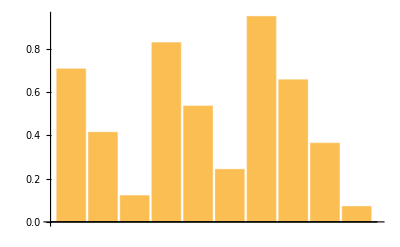

```mathematica
Range@10/√2.
FractionalPart@%//BarChart
```

```mathematica
mat = BoxMatrix[3,9]+DiamondMatrix@4
```

{{0,0,0,0,1,0,0,0,0},{0,1,1,2,2,2,1,1,0},{0,1,2,2,2,2,2,1,0},{0,2,2,2,2,2,2,2,0},{1,2,2,2,2,2,2,2,1},{0,2,2,2,2,2,2,2,0},{0,1,2,2,2,2,2,1,0},{0,1,1,2,2,2,1,1,0},{0,0,0,0,1,0,0,0,0}}

```mathematica
Closing[src, mat/. 2->1]
```

-Graphics-

```mathematica
diamondClosing = Closing[src, DiamondMatrix@10];
Image[%,ImageSize->Scaled@3]
```

-Graphics-

## mesh

```mathematica
reg = ImageMesh[ColorNegate@src, Method->"LinearSeparable"];
```

```mathematica
reg //Head
```

BoundaryMeshRegion

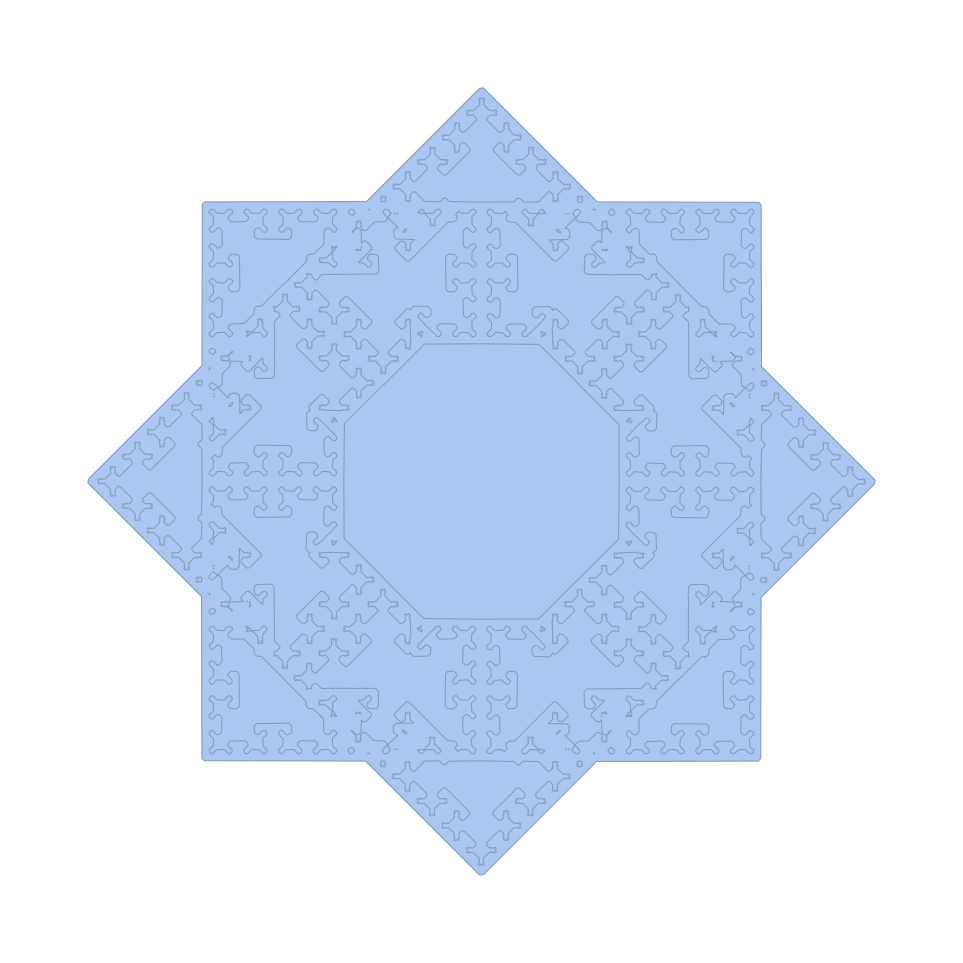

```mathematica
ImageMesh[ColorNegate@diamondClosing, Method->"LinearSeparable"]
```